-x0^4 (1-x0^2)+x1^2

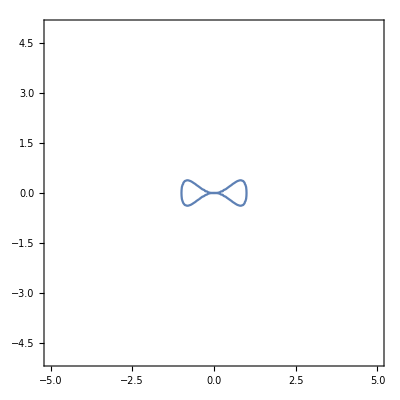

```mathematica
f = x1^2 - x0^4 (1 - x0^2)
ContourPlot[f==0,{x0,-5,5},{x1,-5,5}]
```

-16 u0^6+16 u0^8-729 u1^2+1053 u0^2 u1^2-300 u0^4 u1^2-8 u0^6 u1^2+216 u1^4+132 u0^2 u1^4+u0^4 u1^4-16 u1^6

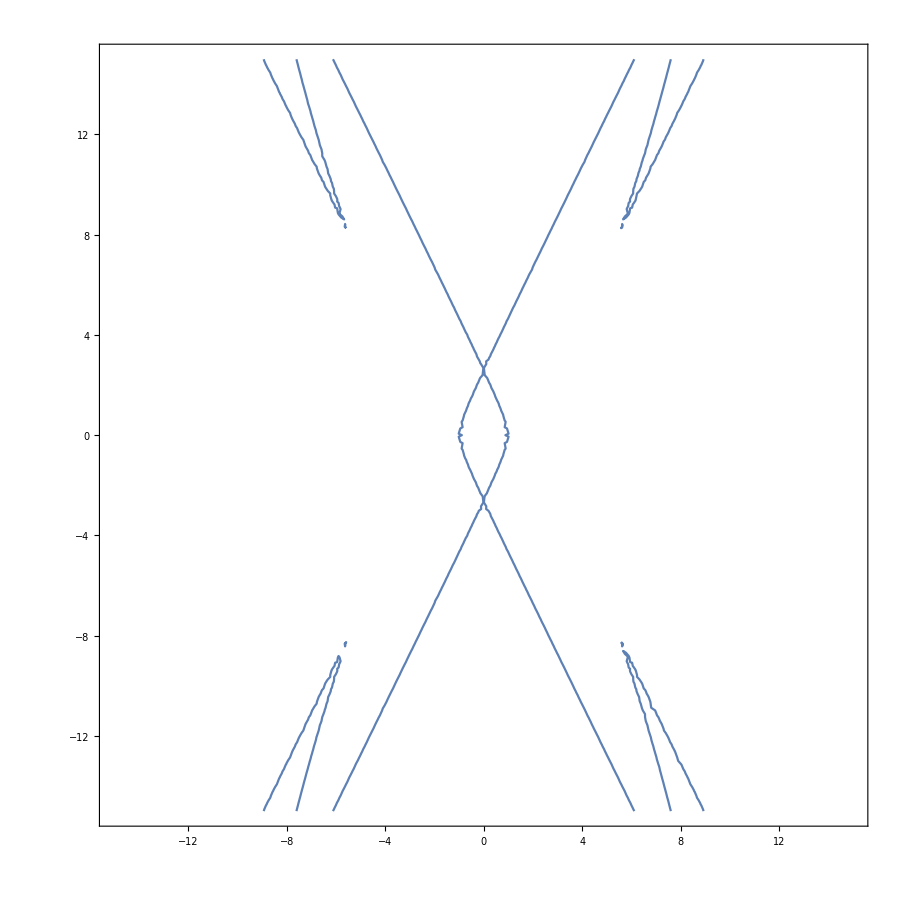

x0^6 - x0^4*x2^2 + x1^2*x2^4

```mathematica
h = ResourceFunction["PolynomialHomogenize"][Expand[f],{x0, x1},x2];
h //InputForm

d = 16*u0^8-8*u0^6*u1^2+u0^4*u1^4-16*u0^6*u2^2-300*u0^4*u1^2*u2^2+132*u0^2*u1^4*u2^2-16*u1^6*u2^2+1053*u0^2*u1^2*u2^4+216*u1^4*u2^4-729*u1^2*u2^6;

s = d /. u2-> 1
ContourPlot[s == 0, {u0, -15, 15}, {u1, -15, 15},MaxRecursion-> 1, PlotPoints-> 100]
```